3.168

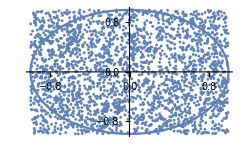

Part::partw: Part 31463 of {0.98914, -0.540996, 0.494398, 0.989374, 0.204777, -0.718032, 0.0802021, -0.966012, -0.847793, 0.0292345, « 31 », 0.553378, 0.212121, -0.85487, -0.291966, -0.614788, -0.49381, 0.360144, 0.274469, 0.525564, « 31412 »} does not exist.

Part::partw: Part 31463 of {-0.21646, -0.518316, 0.653774, 0.41983, -0.484913, -0.00414774, 0.60514, 0.110454, 0.621163, -0.740643, « 31 », 0.307497, -0.881575, -0.310195, 0.856788, -0.591443, 0.719361, -0.909282, 0.268135, -0.265556, « 31412 »} does not exist.

Part::partw: Part 31464 of {0.98914, -0.540996, 0.494398, 0.989374, 0.204777, -0.718032, 0.0802021, -0.966012, -0.847793, 0.0292345, « 31 », 0.553378, 0.212121, -0.85487, -0.291966, -0.614788, -0.49381, 0.360144, 0.274469, 0.525564, « 31412 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
a=0;
b=0;
n=2500;
ContadorCir=0;
ContadorCua=n;
Matriz1={};
Matriz2={};

For[i=1, i<n,i++,
     a=RandomReal[{-1,1}];
     b=RandomReal[{-1,1}];
AppendTo[Matriz1,a];
AppendTo[Matriz2,b];
     If[ a^2+ b^2≤1,ContadorCir++,ContadorCir]
									             ]

Matriz1;
Matriz2;
Datos=Table[{Matriz1[[i]],Matriz2[[i]]},{i,1,n-1}];

MiPi= (4*ContadorCir)/ContadorCua//N

Puntos=ListPlot[Datos];
Circulo=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*π}];
Show[Puntos,Circulo]
```